{{3.51155,-4.82831},{Log[42],-4.71053},{Log[54],-4.71053},{Log[60],-4.50986},{Log[71],-4.71053},{Log[77],-6.90776},{Log[81],-7.01312},{4.44852,-∞},{Log[88],-6.50229},{Log[94],-∞}}

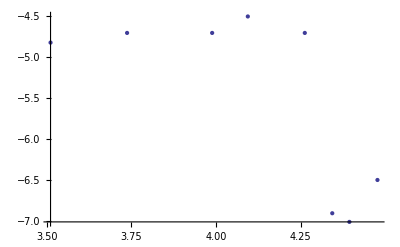

```mathematica
werte:={{33.5,0.008},{42,0.009},{54,0.009},{60,0.011},{71,0.009},{77,0.001},{81,0.0009},{85.5,0},{88,0.0015},{94,0}};
werteLn={};
For[i=1,i≤Length[werte],i++,AppendTo[werteLn,{Log[werte[[i]][[1]]], Log[werte[[i]][[2]]]}]]

ListPlot[werteLn,AxesLabel->{"Ln(T) [Ln(°C)]", "Ln(U_P) [Ln(mV)]"]
```